```mathematica
SetDirectory["C:\\Users\\griho\\OneDrive\\Рабочий стол\\Практика\\Программа\\project"];
points=ReadList["question1.txt",Real];
points//MatrixForm;
numberOfPoints = IntegerPart[points[[1]]];
points = Delete[points,1];
points=Partition[points,2];
points;

convexHullPoints = {};
```

```mathematica
determinePointPosition[lineStartPoint_,lineEndPoint_,pointToCheck_]:=
Module[{result,positionFromTheLine},
result:=(pointToCheck[[1]]-lineStartPoint[[1]])*(lineEndPoint[[2]]-lineStartPoint[[2]])-(pointToCheck[[2]]-lineStartPoint[[2]])*(lineEndPoint[[1]]-lineStartPoint[[1]]);
positionFromTheLine:=Which[result<0,"one side",result>0,"other side",result==0,"within" ]; positionFromTheLine]
```

```mathematica
If[Length[points]==0,Print["There are no points in the txt file or there is a problem with reading it. Execution stopped";Abort]];
```

```mathematica
IneffectiveConvexHull[Points_List] :=
 Module[{pointWithXmax,formerPoint,latterPoint,areOnTheSameSide,comparator,currentPointPosition,indexOfElementWithMaxXCoord,i,indexInPoints},
For[i= 2;indexOfElementWithMaxXCoord=1, i≤ numberOfPoints, i+=1,
If[points⟦i,1⟧>points⟦indexOfElementWithMaxXCoord,1⟧,indexOfElementWithMaxXCoord=i;indexOfElementWithMaxXCoord]];
pointWithXmax=points[[indexOfElementWithMaxXCoord]];
points=Delete[points,indexOfElementWithMaxXCoord];
PrependTo[points,pointWithXmax];
AppendTo[convexHullPoints,pointWithXmax];
formerPoint=convexHullPoints[[Length[convexHullPoints]]];
For[i=2,i≤ Length[points],++i, 
latterPoint=points[[i]];
areOnTheSameSide=True;
indexInPoints=1;
comparator="within";

For[indexInPoints=1,indexInPoints≤ Length[points], ++indexInPoints,

If[comparator≠ "within",++indexInPoints;Break[];(*Print["If",comparator]*),
Null];
comparator=determinePointPosition[formerPoint,latterPoint,points[[indexInPoints]]];
];
For[Null,indexInPoints≤ Length[points], ++indexInPoints, 
currentPointPosition=determinePointPosition[formerPoint,latterPoint,points[[indexInPoints]]];
If[((currentPointPosition≠comparator)&&(currentPointPosition≠"within")),
areOnTheSameSide=False;Break[], 
Null]
];
If[((areOnTheSameSide)&& !(MemberQ[convexHullPoints,latterPoint])),
 AppendTo[convexHullPoints,latterPoint];
formerPoint=latterPoint;
i=0,
Null]
];
AppendTo[convexHullPoints,convexHullPoints[[1]]];
Graphics[{Point@Points, Line@convexHullPoints}]
]
```

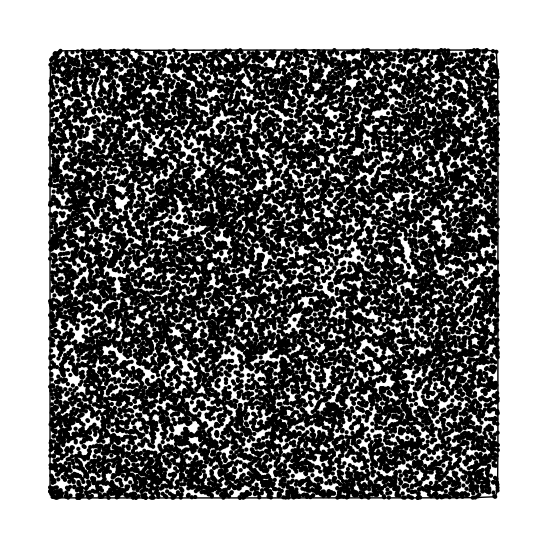
{99.8281,-Graphics-}

```mathematica
Timing@IneffectiveConvexHull[points]
```

```mathematica
convexHullPoints
```

{{0.999939,0.669118},{0.998535,0.879147},{0.99292,0.992187},{0.977905,0.995178},{0.947996,0.999878},{0.74633,0.999878},{-0.150487,0.999573},{-0.778008,0.998474},{-0.953185,0.996216},{-0.976562,0.986145},{-0.979431,0.98291},{-0.993957,0.958617},{-0.997986,0.933958},{-0.999451,0.75164},{-0.999939,0.609363},{-0.999939,-0.952757},{-0.999817,-0.971618},{-0.988647,-0.995361},{-0.972106,-0.999573},{-0.878353,-0.999756},{-0.616504,-1.},{0.641957,-0.999634},{0.887692,-0.998901},{0.987671,-0.994629},{0.998169,-0.966674},{0.999634,-0.786554},{0.999756,-0.763787},{0.999939,0.532334},{0.999939,0.669118}}

```mathematica
Length[convexHullPoints]
```

29